```mathematica
Ts=1;R=4;Np=25;
```

```mathematica
xd1[n_]=Boole[0<=n<=Np-1]*Sin[2Pi*n/12];
```

```mathematica
xd2[n_]=Boole[0<=n<=R*Np-1]*Boole[Divisible[n,R]]*xd1[Quotient[n,R]];
```

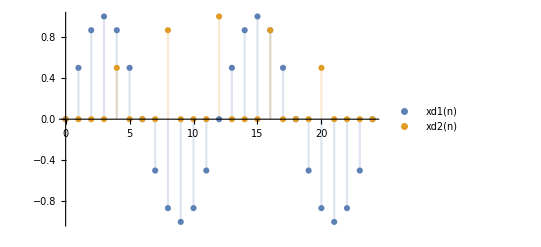

```mathematica
DiscretePlot[{xd1[n],xd2[n]},{n,0,Np-1},PlotLegends->"Expressions"]
```

```mathematica
array xd1=Table[xd1[n],{n,0,Np-1}];
```

```mathematica
array xd2=Table[xd2[n],{n,0,R*Np-1}];
```

```mathematica
x1[t_]=Boole[0<=t<=Np*Ts]*Indexed[array xd1,1+Quotient[t,Ts]];
```

```mathematica
x2[t_]=Boole[0<=t<=Np*Ts]*Indexed[array xd2,1+Quotient[t,Ts/R]];
```

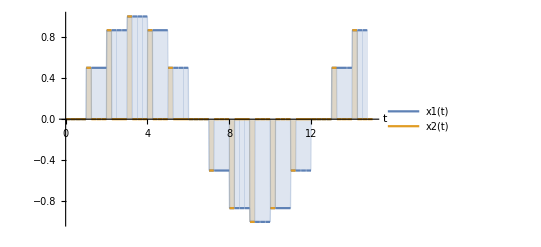

```mathematica
Plot[{x1[t],x2[t]},{t,0,15},Filling->Axis,PlotPoints->1+Np,AxesLabel->Automatic,PlotLegends->"Expressions"]
```

```mathematica
Xd1[ω_]=FullSimplify[Sum[xd1[n]*Exp[-I*ω*n*Ts],{n,0,Np-1}]]
```

-ⅈ ⅇ^(-12 ⅈ ω) (√3+2 Cos[ω]) (Sin[2 ω]+Sin[4 ω]-Sin[8 ω]-Sin[10 ω])

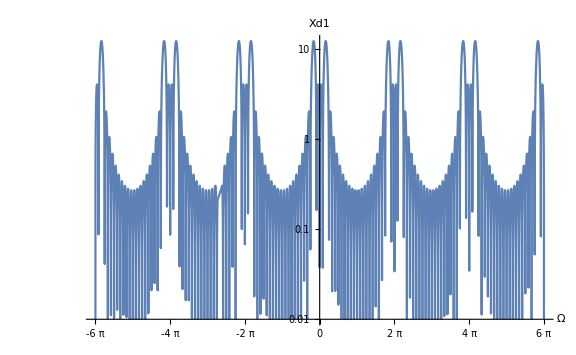

```mathematica
Block[{K=6},LogPlot[Abs[Xd1[Ω/Ts]],{Ω,-K*Pi,K*Pi},PlotRange->{1/100,Automatic},PlotPoints->100,AxesLabel->Automatic,Ticks->{Table[k*Pi,{k,-K,K}],Automatic},PlotLabel->"Xd1",ImageSize->Large]]
```

```mathematica
X1[ω_]=FullSimplify[Integrate[x1[t]*Exp[-I*ω*t],{t,0,Np*Ts}]/Sqrt[2Pi]]
```

1/ω 2 ⅈ ⅇ^(-(25 ⅈ ω)/2) √(2/π) (√3+2 Cos[ω]) (Cos[(5 ω)/2]+Cos[(7 ω)/2]+2 Cos[(9 ω)/2]+2 Cos[(11 ω)/2]+2 Cos[(13 ω)/2]+2 Cos[(15 ω)/2]+Cos[(17 ω)/2]+Cos[(19 ω)/2]) Sin[ω/2]^2

```mathematica
$MaxPiecewiseCases=150;
X2[ω_]=FullSimplify[Integrate[x2[t]*Exp[-I*ω*t],{t,0,Np*Ts}]/Sqrt[2Pi]];
$MaxPiecewiseCases=100;
```

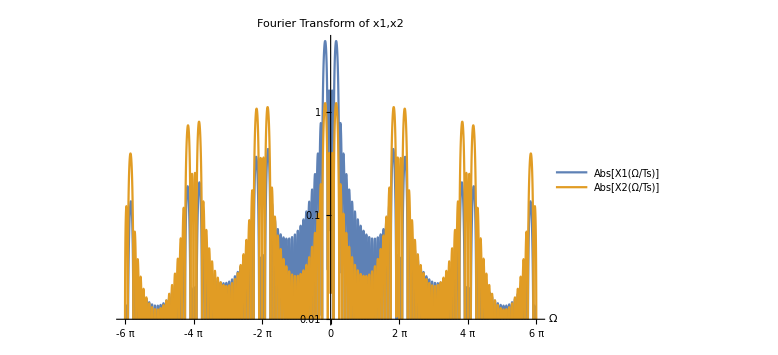

```mathematica
Block[{K=6},LogPlot[{Abs[X1[Ω/Ts]],Abs[X2[Ω/Ts]]},{Ω,-K*Pi,K*Pi},PlotRange->{1/100,Automatic},PlotPoints->150,AxesLabel->Automatic,Ticks->{Table[k*Pi,{k,-K,K}],Automatic},PlotLabel->"Fourier Transform of x1,x2",PlotLegends->"Expressions",ImageSize->Large]]
```